Target export directory: If[G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\Vector_Electrostatics_v4.nb≠$Failed,NotebookDirectory[],$HomeDirectory]

--- Task 1.1 ---

A x B = {-z (y^2+x z),z (x^2-y z),x^3+y^3}

curl A = {0,0,-2}

curl B = {0,0,0}

curl(grad phi) = {0,0,0}

--- Task 1.2 ---

div F (for r != 0) = 0

Export::chtype: 第一个参数 FileNameJoin[{If[G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\Vector_Electrostatics_v4.nb≠$Failed,NotebookDirectory[],$HomeDirectory],vector_plot_f.png}] 不是一个有效的文件指定.

Vector plot saved at: FileNameJoin[{If[G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\Vector_Electrostatics_v4.nb≠$Failed,NotebookDirectory[],$HomeDirectory],vector_plot_f.png}]

--- Task 2 ---

Export::chtype: 第一个参数 FileNameJoin[{If[G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\Vector_Electrostatics_v4.nb≠$Failed,NotebookDirectory[],$HomeDirectory],potential_contour.png}] 不是一个有效的文件指定.

Export::chtype: 第一个参数 FileNameJoin[{If[G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\Vector_Electrostatics_v4.nb≠$Failed,NotebookDirectory[],$HomeDirectory],field_stream.png}] 不是一个有效的文件指定.

Images saved in: If[G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\Vector_Electrostatics_v4.nb≠$Failed,NotebookDirectory[],$HomeDirectory]

--- Visual Results ---

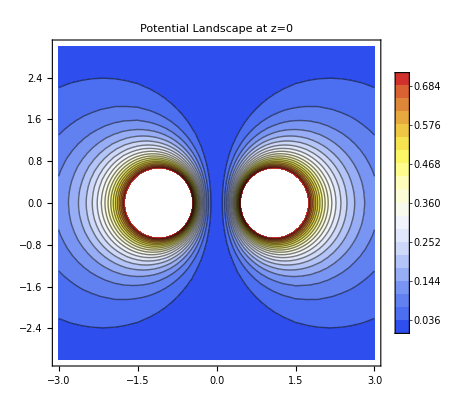

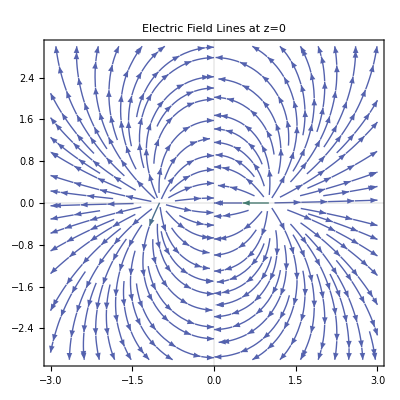

Finding equilibrium points (Optimized Symbolic Search)...

Equilibrium points (E=0): y→0 | z→-0.620721 | x→0
y→0 | z→-0.620721 | x→0
y→0 | z→-0.620721 | x→0
y→0 | z→-0.620721 | x→0

```mathematica
(*Configuration:Set export directory*)(*If you haven't saved your notebook,this will use the system default directory*)exportDir=If[NotebookFileName[]!=$Failed,NotebookDirectory[],$HomeDirectory];
Print["Target export directory: ",exportDir];

(*Task 1.1:Vector Calculus*)
Print["--- Task 1.1 ---"];
A={y,-x,z};
B={x^2,y^2,z^2};

(*Cross Product*)
crossAB=Cross[A,B]//Simplify;
Print["A x B = ",crossAB];

(*Curl*)
curlA=Curl[A,{x,y,z}];
curlB=Curl[B,{x,y,z}];
Print["curl A = ",curlA];
Print["curl B = ",curlB];

(*Identity:curl(grad phi)=0*)
phiScalar=f[x,y,z];
gradPhi=Grad[phiScalar,{x,y,z}];
curlGradPhi=Curl[gradPhi,{x,y,z}]//Simplify;
Print["curl(grad phi) = ",curlGradPhi];


(*Task 1.2:Divergence and Flux*)
Print["\n--- Task 1.2 ---"];
r=Sqrt[x^2+y^2+z^2];
F={x,y,z}/r^3;

divF=Div[F,{x,y,z}]//FullSimplify;
Print["div F (for r != 0) = ",divF];

(*Visualization*)
vectorPlot=VectorPlot3D[F,{x,-2,2},{y,-2,2},{z,-2,2},VectorPoints->10,VectorStyle->"Arrow3D",PlotLabel->"Field F = r/r^3",PlotTheme->"Scientific"];
Export[FileNameJoin[{exportDir,"vector_plot_f.png"}],vectorPlot,ImageSize->800];
Print["Vector plot saved at: ",FileNameJoin[{exportDir,"vector_plot_f.png"}]];

(*Physical Interpretation:This field represents the electric field of a point charge at the origin (or the gravitational field of a point mass).Divergence is zero everywhere except at the origin.*)


(*Task 2:Electrostatics*)
Print["\n--- Task 2 ---"];
q=1;k=1;
charges={{q,{1,0,0}},{q,{-1,0,0}},{-2*q,{0,0,1}}};

(*Total Potential phi(x,y,z)*)
phiTotal[x_,y_,z_]:=Sum[c[[1]]/Sqrt[(x-c[[2,1]])^2+(y-c[[2,2]])^2+(z-c[[2,3]])^2],{c,charges}];

(*Electric Field E=-grad phi*)
fieldE[x_,y_,z_]:=-Grad[phiTotal[sx,sy,sz],{sx,sy,sz}]/. {sx->x,sy->y,sz->z};

(*Visualizations on z=0 plane*)
contourPlot=ContourPlot[phiTotal[x,y,0],{x,-3,3},{y,-3,3},Contours->20,ColorFunction->"TemperatureMap",PlotLabel->"Potential Landscape at z=0",PlotTheme->"Detailed"];
streamPlot=StreamPlot[Take[fieldE[x,y,0],2],{x,-3,3},{y,-3,3},PlotLabel->"Electric Field Lines at z=0",PlotTheme->"Scientific"];

(*Export images*)
Export[FileNameJoin[{exportDir,"potential_contour.png"}],contourPlot,ImageSize->800];
Export[FileNameJoin[{exportDir,"field_stream.png"}],streamPlot,ImageSize->800];
Print["Images saved in: ",exportDir];

(*Display plots directly in Notebook with labeling*)
Print["--- Visual Results ---"];
Show[contourPlot]
Show[streamPlot]

(*Optimized:Compute symbolic gradient once to avoid re-computation*)
symbolicPhi=phiTotal[sx,sy,sz];
symbolicE=-Grad[symbolicPhi,{sx,sy,sz}]//Simplify;

(*Find equilibrium points E=0*)
Print["Finding equilibrium points (Optimized Symbolic Search)..."];
(*Solve using the pre-computed symbolic expressions*)
eqPoints=NSolve[Thread[(symbolicE/. {sx->x,sy->y,sz->z})==0]~Join~{-2<x<2,-2<y<2,-2<z<2},{x,y,z},Reals];

Print["Equilibrium points (E=0): ",eqPoints//TableForm];

(*Stability Discussion:Equilibrium points in static electric fields are always unstable (saddle points) due to Gauss's Law (Earnshaw's Theorem).*)
```